#### Step H: Histogram plots

```mathematica
filenameVolumeBase="FR96D1_"; 
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

{309,566,374}

```mathematica
100*Max[concFR]
```

7.07778

```mathematica
SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFR],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{4244.,Null}

60108823

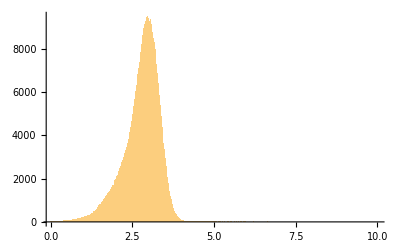

2.77894

0.53676

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,10,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
(*______________________________________*)
```

```mathematica
filenameVolumeBase="FR96D1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

```mathematica
Dimensions[concSb2O3]
100*Max[concSb2O3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{309,566,374}

10.5528

{1089.36,Null}

57909428

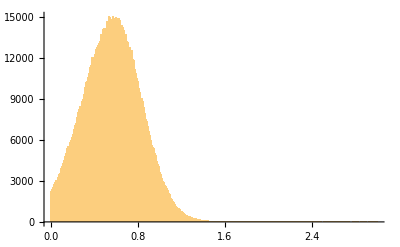

0.571131

0.273197

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,3,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
--------------------------------------------------------------------------------------
```

```mathematica
(*concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]*)
```

```mathematica
(*100*Max[concFR]
```

```mathematica
(*SeedRandom[1];
Histogram[RandomSample[100*Flatten[concFR],100000],{1.0,8,0.1}]*)
```

```mathematica
(*sliceFR = Take[concFR,{128},{300,600},{600,800}];
sliceFR = Take[concFR,{128},{400,600},{400,700}];
Dimensions[sliceFR]
sliceFR =sliceFR[[1]];
Dimensions[sliceFR]
Image[sliceFR,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceFR],{0.0,10,0.1}]*)
```

```mathematica
(*concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3]*)
```

```mathematica
(*100*Max[concSb2O3]*)
```

```mathematica
(*sliceSb2O3 = Take[concSb2O3,{128},{300,600},{600,800}];
sliceSb2O3 = Take[concSb2O3,{128},{400,600},{400,700}];
Dimensions[sliceSb2O3]
sliceSb2O3 =sliceSb2O3[[1]];
Dimensions[sliceSb2O3]
Image[sliceSb2O3,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceSb2O3],{0.1,2,0.1}]
100*Max[sliceSb2O3]*)
```

```mathematica
(*dataFRandSb2O3 = Transpose[{100*Flatten[sliceFR],100*Flatten[sliceSb2O3]}];
Dimensions[dataFRandSb2O3]
Histogram3D[dataFRandSb2O3,{{0.1,10,0.1},{0.1,2,0.05}},ChartElementFunction->"GradientScaleCube"]*)
```

Green Armor BFR vol% Histograms (E, F, G1 and G2)

```mathematica
filenameVolumeBase="FR96E1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/"
concFRE1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRE1]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/

{256,723,705}

```mathematica
filenameVolumeBase="FR96F1_";
concFRF1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRF1]
```

{256,631,612}

```mathematica
filenameVolumeBase="FR96G1_";
concFRG1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRG1]
```

{256,352,615}

```mathematica
filenameVolumeBase="FR96G2_";
concFRG2=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRG2]
```

{256,611,507}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concFRE1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRE1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRE1]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFRF1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRF1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRF1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRG1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRG2],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG2 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG2]
```

{73.4658,Null}

79321971

1000000

{56.2365,Null}

61869601

1000000

{31.9901,Null}

24492316

1000000

{43.0665,Null}

38028682

1000000

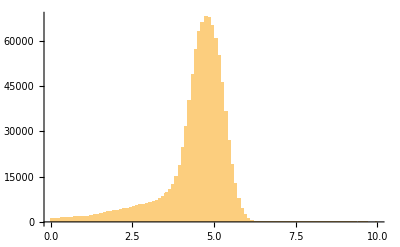

4.4372

0.982033

```mathematica
Histogram[concFRG1,{0.0,10,0.1}]
Mean[concFRG1]
StandardDeviation[concFRG1]
```

```mathematica
list =HistogramList[concFRG2,{0.0,100,0.1}];
threshold=5.2;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

53

291522.

4.65641×10^6

6.26067

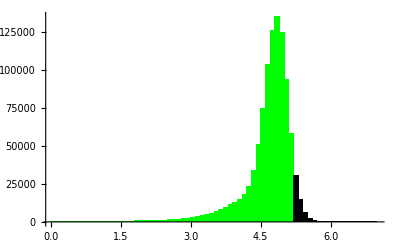

```mathematica
listBelowThreshold = Histogram[Select[concFRG2,#<threshold &],{0.0,7,0.1},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concFRG2,#>=threshold &],{0,7,0.1},ChartStyle->Directive[Black,EdgeForm[]]];
gFRG2=Show[{listBelowThreshold,listAboveThreshold}]
```

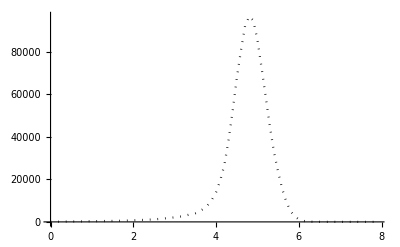

```mathematica
data =HistogramList[concFRE1,{0,8,0.1}];
gFRE1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]]
```

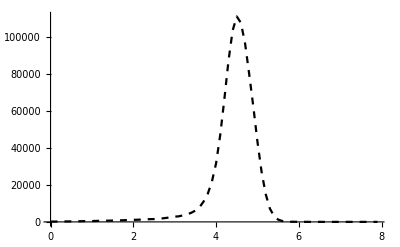

```mathematica
data =HistogramList[concFRF1,{0,8,0.1}];
gFRF1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]]
```

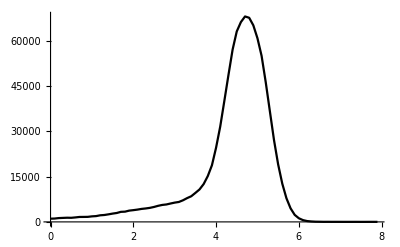

```mathematica
data =HistogramList[concFRG1,{0,8,0.1}];
gFRG1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]]
```

```mathematica
{gFRE1,gFRF1,gFRG1}
```

{-Graphics-,-Graphics-,-Graphics-}

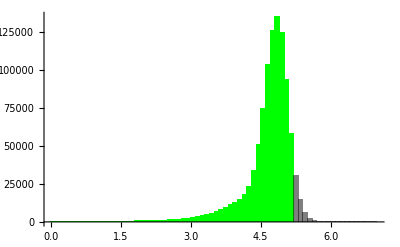

```mathematica
gHistG2=Histogram[{
Select[concFRG2,#<threshold &],
Select[concFRG2,#>=threshold &]},{0,7,.1},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

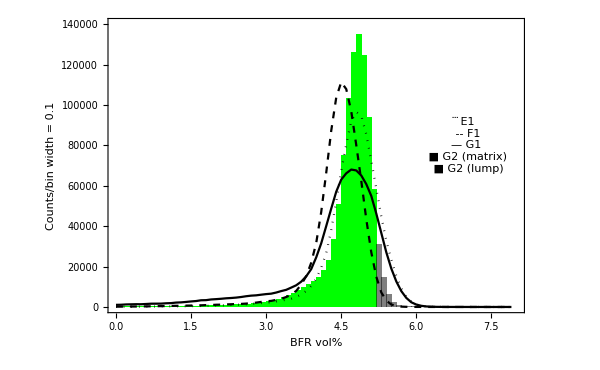

```mathematica
Show[{gHistG2,gFRE1,gFRF1,gFRG1},PlotRange->{{0,8},{0,140000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"Counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ E1\n -- F1\n— G1\n ■ G2 (matrix)\n ■ G2 (lump)"],{7.0,80000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"E1", Mean[concFRE1],StandardDeviation[concFRE1],Max[concFRE1]},
{"F1", Mean[concFRF1],StandardDeviation[concFRF1],Max[concFRF1]},
{"G1", Mean[concFRG1],StandardDeviation[concFRG1],Max[concFRG1]},
{"G2", Mean[concFRG2],StandardDeviation[concFRG2],Max[concFRG2]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"G2", threshold,fractionBFRinlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
E1 | 4.77852 | 0.598483 | 20.3507
F1 | 4.47336 | 0.565794 | 14.4457
G1 | 4.4372 | 0.982033 | 13.886
G2 | 4.6564 | 0.547778 | 14.1878

sample | threshold | fraction in lumps
G2 | 5.2 | 6.26067

```mathematica
(*Show[{gFRE1,gFRF1,gFRG1},PlotRange->{{0,8},{0,140000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ E1\n -- F1\n— G1"],{7.0,80000}],16,TextAlignment->Right]]*)
```

Sb2O3 plots Green Armor

```mathematica
filenameVolumeBase="FR96A1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/"
concSb2O3A1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3A1]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/

{300,318,500}

```mathematica
filenameVolumeBase="FR96F1_";
concSb2O3F1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3F1]
```

{256,631,612}

```mathematica
filenameVolumeBase="FR96G1_";
concSb2O3G1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3G1]
```

{256,352,615}

```mathematica
filenameVolumeBase="FR96G2_";
concSb2O3G2=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3G2]
```

{256,611,507}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concSb2O3A1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3A1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3A1]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3F1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3F1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3F1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3G1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3G1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3G1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3G2],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3G2 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3G2]
```

{28.1817,Null}

47533860

1000000

{56.0785,Null}

50945545

1000000

{31.8092,Null}

24189793

1000000

{42.7735,Null}

37798740

1000000

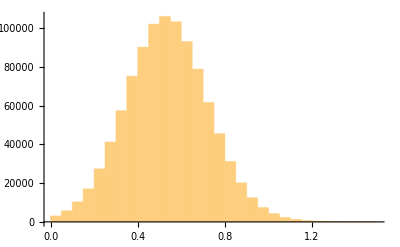

0.536193

0.193723

```mathematica
Histogram[concSb2O3A1,{0.0,1.5,0.05}]
Mean[concSb2O3A1]
StandardDeviation[concSb2O3A1]
```

```mathematica
list =HistogramList[concSb2O3A1,{0.0,100,0.05}];
threshold=0.8;  (* based on A1 *)
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionSb2O3inlumps = 100*volPercentNumerator/volPercentDenominator
```

17

73404.4

536198.

13.6898

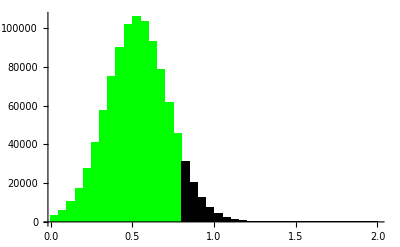

```mathematica
listBelowThreshold = Histogram[Select[concSb2O3A1,#<threshold &],{0,2,0.05},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concSb2O3A1,#>=threshold &],{0,2,0.05},ChartStyle->Directive[Black,EdgeForm[]]];
gSb2O3A1=Show[{listBelowThreshold,listAboveThreshold}]
```

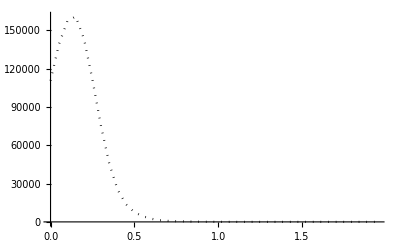
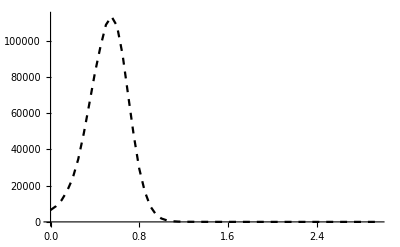
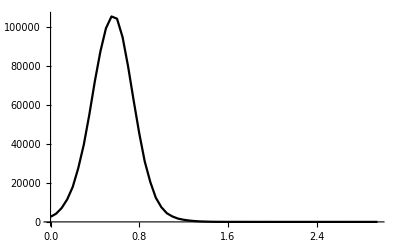

```mathematica
data =HistogramList[concSb2O3F1,{0,2,0.05}];
gSb2O3F1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concSb2O3G1,{0,3,0.05}];
gSb2O3G1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concSb2O3G2,{0,3,0.05}];
gSb2O3G2 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gSb2O3F1,gSb2O3G1,gSb2O3G2}
```

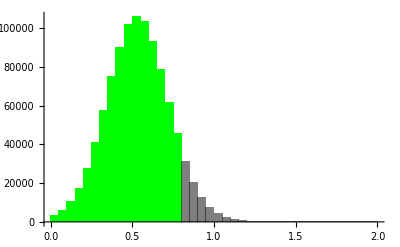

```mathematica
gHistA1=Histogram[{
Select[concSb2O3A1,#<threshold &],
Select[concSb2O3A1,#>=threshold &]},{0,2,0.05},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

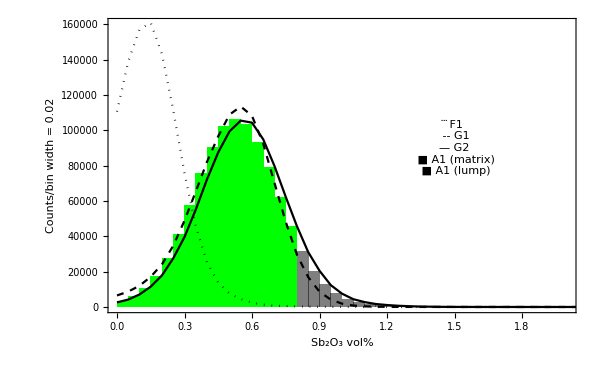

```mathematica
Show[{gHistA1,gSb2O3F1,gSb2O3G1,gSb2O3G2},PlotRange->{{0,2.0},{0,160000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"Counts/bin width = 0.02",""},{"Sb_2O_3 vol%",""}},
Epilog->Style[Text[Framed[" ⃛ F1\n -- G1\n— G2\n ■ A1 (matrix)\n ■ A1 (lump)"],{1.5,90000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"A1", Mean[concSb2O3A1],StandardDeviation[concSb2O3A1],Max[concSb2O3A1]},
{"G1", Mean[concSb2O3G1],StandardDeviation[concSb2O3G1],Max[concSb2O3G1]},
{"G2", Mean[concSb2O3G2],StandardDeviation[concSb2O3G2],Max[concSb2O3G2]},
{"F1", Mean[concSb2O3F1],StandardDeviation[concSb2O3F1],Max[concSb2O3F1]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"A1", threshold,fractionSb2O3inlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
A1 | 0.536193 | 0.193723 | 10.0555
G1 | 0.537461 | 0.187158 | 10.0671
G2 | 0.586202 | 0.199532 | 14.1532
F1 | 0.193039 | 0.122705 | 2.48188

sample | threshold | fraction in lumps
A1 | 0.8 | 13.6898